```mathematica
e[t_]:=87.740-(0.40008*t)+(0.0009398*(t^2))-(0.000001410*(t^3))
```

```mathematica
data=Table[{t,e[t]},{t,0,100}];
ListLinePlot[data];
nlm=NonlinearModelFit[data,a-(b*t)+(c*(t^2))-(d*(t^3)),{a,b,c,d},t];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 87.74 | 5.9626×10^-15 | 1.47151×10^16 | 9.83862876671156×10^-1474
b | 0.40008 | 5.18953×10^-16 | 7.70937×10^14 | 1.67886209573971×10^-1349
c | 0.0009398 | 1.20932×10^-17 | 7.77133×10^13 | 7.72322336646617×10^-1253
d | 1.41×10^-6 | 7.94723×10^-20 | 1.7742×10^13 | 1.29577141115319×10^-1190

```mathematica
{x,y}=Transpose[data];
```

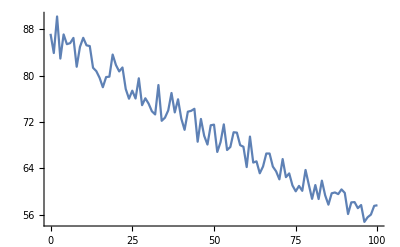

```mathematica
(* pseudo 5% error *)
ywitherror=Table[y[[ii]]+RandomReal[{-Floor[y[[ii]]*0.05],Floor[y[[ii]]*0.05]}],{ii,1,Length[y]}];
datawitherror = Transpose[{x,ywitherror}];
ListLinePlot[datawitherror]
```